# EIWL Sections 47 and 48

## 8/8 Due to getting a little behind in the final two weeks of the semester, I only checked for completeness on PS 18-21. ~Brian

# Problem Set 21

## Section 47

```mathematica
Total[Table[i*(i+1),{i,1000}]]
```

334334000

```mathematica
Nest[1/(1+#)&,x,10]
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))

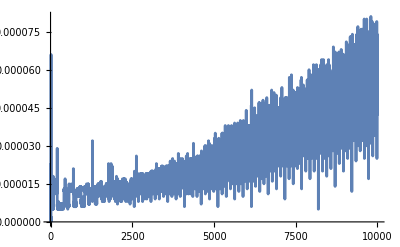

```mathematica
ListLinePlot[Table[Timing[n^n][[1]],{n,10000}]]
```

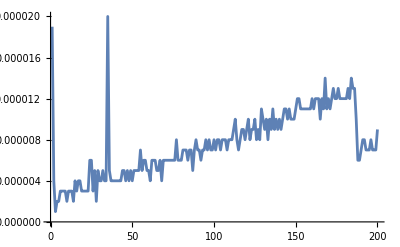

```mathematica
ListLinePlot[Table[Timing[Sort[RandomSample[Range[n]]]][[1]],{n,200}]]
```

## Section 48

```mathematica
Counts[If[StringLength[#]>1,StringTake[#,2],Nothing[]]&/@WordList[]]
```

<|aa→2,ab→170,ac→217,ad→191,ae→26,af→72,ag→81,ah→5,ai→55,AI→1,aj→1,ak→2,al→204,am→139,an→330,ao→3,ap→165,Ap→1,aq→14,ar→207,as→198,AS→1,at→99,au→117,Au→1,av→46,aw→30,ax→12,ay→2,az→4,ba→448,BA→1,be→359,bi→208,bl→254,bo→302,br→306,bu→255,by→14,ca→612,ce→126,ch→442,ci→89,cl→265,cn→1,co→1589,CO→1,cr→337,cu→184,cy→45,cz→3,da→152,dB→1,de→884,De→1,dh→2,di→827,DN→1,do→244,DO→1,dr→172,du→113,dw→9,dy→29,ea→72,eb→7,ec→45,ed→39,ee→4,e'→2,ef→45,eg→28,eh→1,ei→16,ej→3,el→136,em→144,en→316,eo→1,ep→53,eq→41,er→56,es→63,et→42,eu→25,ev→76,ew→2,ex→416,ey→21,fa→276,fe→174,Fe→1,fi→251,fj→1,fl→266,fo→335,FO→1,fr→228,Fr→1,fu→138,ga→193,ge→153,gh→15,gi→65,gl→136,gn→13,go→124,Go→1,gr→347,gu→120,gy→19,ha→363,he→321,hi→127,HI→1,h'→1,hm→1,ho→340,hu→134,hy→116,ia→4,ib→4,ic→27,id→55,if→2,ig→18,il→54,im→324,in→1244,io→10,ip→1,IQ→1,ir→90,is→36,it→17,iv→3,ja→72,Ja→1,je→47,ji→32,jo→76,ju→86,Ju→2,ka→20,kc→1,ke→40,kh→3,kH→1,ki→88,kl→4,kn→51,ko→10,kp→1,kr→5,ku→3,kv→1,kW→1,la→301,le→224,li→293,ll→2,lo→226,lu→102,ly→20,ma→589,Ma→2,me→363,mi→409,mn→2,mo→392,Mo→1,ms→1,mu→206,my→33,na→129,ne→208,ni→87,no→304,No→1,nt→1,nu→86,ny→4,oa→15,ob→126,oc→46,o'→2,Oc→1,od→19,oe→2,of→47,og→3,oh→5,oi→12,ok→3,ol→20,om→19,on→34,oo→7,op→86,or→114,os→28,ot→7,ou→125,ov→215,ow→11,ox→19,oy→1,oz→1,pa→553,pe→487,pf→1,pH→1,ph→160,pi→217,pl→228,pn→4,po→402,pr→815,ps→50,pt→3,pu→225,py→22,qu→194,ra→307,re→1228,rh→39,ri→148,ro→206,ru→122,ry→1,sa→321,Sa→1,sc→334,se→552,Se→1,sh→377,si→241,sk→94,sl→196,sm→77,sn→115,so→300,sp→400,sq→56,st→697,su→519,Su→1,sv→1,sw→119,sy→100,ta→270,te→313,th→283,Th→1,ti→167,TN→1,to→253,tr→476,ts→3,tu→119,Tu→1,TV→1,tw→49,ty→42,ub→2,ud→1,UF→1,ug→3,uk→2,ul→24,um→14,un→1335,UN→1,up→75,ur→36,us→25,ut→18,uv→2,ux→1,va→143,ve→170,vi→214,VI→1,vo→84,vu→15,wa→252,we→127,We→1,wh→165,wi→186,wo→166,wr→68,xe→6,xi→1,xy→3,ya→26,ye→36,yi→6,yo→27,yt→2,yu→7,za→3,ze→19,zi→15,zl→1,zo→13,zu→1,zw→1,zy→3|>

```mathematica
Reap[Fold[10Sow[#1]+#2&,{1,2,3,4,5}]][[2]]//Flatten
```

{1,12,123,1234}

```mathematica
Reap[Nest[If[EvenQ[#],Sow[#]/2,3#+1]&,1000,20]][[2]]//Flatten
```

{1000,500,250,376,188,94,142,214,322,484,242,364,182}